```mathematica
Det@{{1,0},{1,0}}
```

0

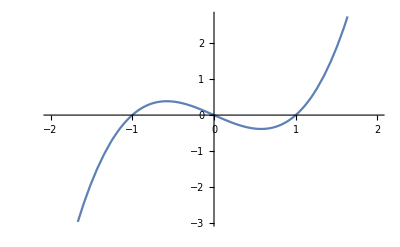

```mathematica
Plot[x x x-x,{x,-2,2}]
```

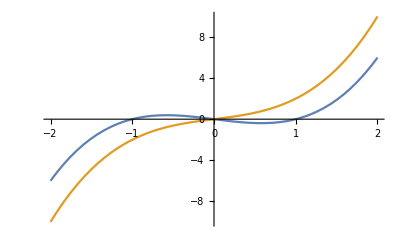

```mathematica
Plot[{x x x-x,x x x+x},{x,-2,2}]
```

```mathematica
Det@{{1,1},{0,0}}
```

0

```mathematica
Det@IdentityMatrix[2]
```

1

```mathematica
IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
Det@{{1,0},{0,-1}}
```

-1

```mathematica
Plot3D[(x-3 y^2)/(x^2-y),{x,y}∈Disk[{0,0},3]]
```

-Graphics3D-

```mathematica
-(x-3 y^2)/(x^2-y)Log[(x-3 y^2)/(x^2-y)]
```

-((x-3 y^2) Log[(x-3 y^2)/(x^2-y)])/(x^2-y)

```mathematica
Plot3D[-((x-3 y^2) Log[(x-3 y^2)/(x^2-y)])/(x^2-y),{x,-0.5291880124805688,2.942597043968733},{y,-0.1481828718676922,1.4534549866250455}]
```

-Graphics3D-

```mathematica
FullSimplify[Normalize@{x,x^2},x∈Reals]
```

{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}

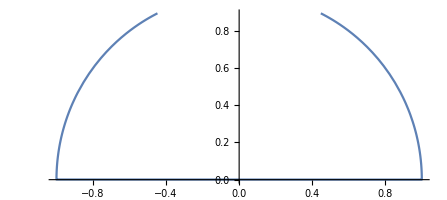

```mathematica
ParametricPlot[
{x/(√(x^2+x^4)),Abs[x]/(√(1+x^2))}
,{x,-2,2}]
```

```mathematica
PolarPlot[Sin[θ],{x,-2,2}]
```

-Graphics-

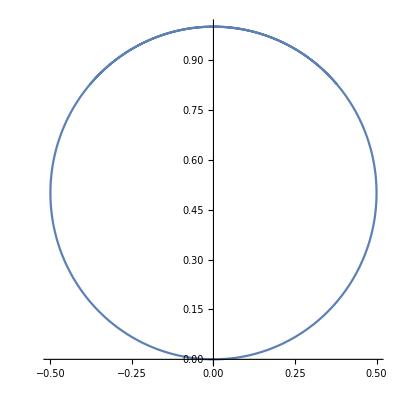

```mathematica
PolarPlot[Sin[θ],{θ,-2,2}]
```

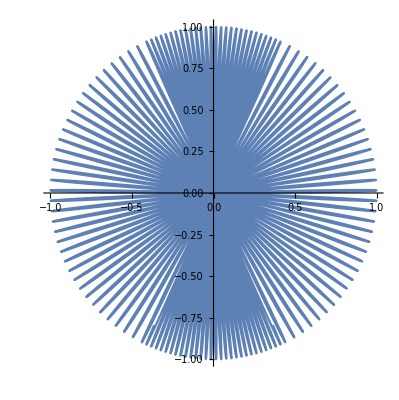

```mathematica
PolarPlot[Sin[100θ],{θ,-2,2}]
```

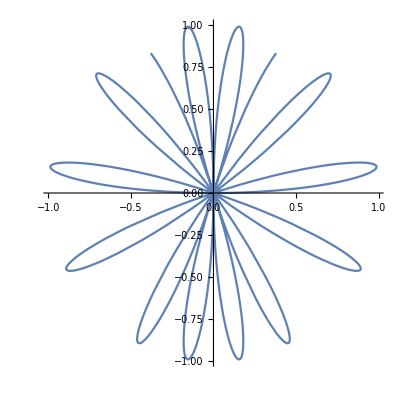

```mathematica
PolarPlot[Sin[10θ],{θ,-2,2}]
```

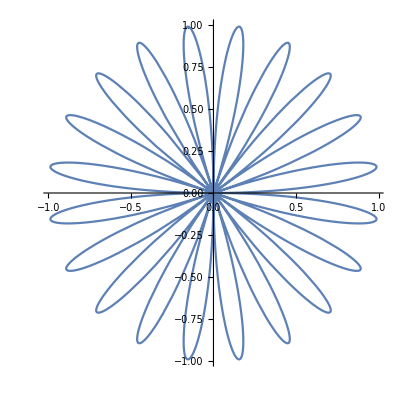

```mathematica
PolarPlot[Sin[10θ],{θ,0,2π}]
```

```mathematica
FullSimplify[Normalize@{x,x^2}.Normalize@{x,x},x∈Reals]
```

(1+x)/(√2 √(1+x^2))

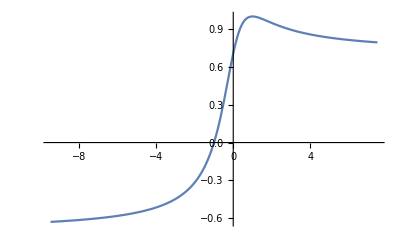

```mathematica
Plot[(1+x)/(√2 √(1+x^2)),{x,-9.493333333333336,7.493333333333335}]
```

```mathematica
Integrate[(1+x)/(√2 √(1+x^2)),{x,-2,2}]
```

√2 ArcSinh[2]

```mathematica
N[√2 ArcSinh[2]]
```

2.04161

```mathematica
Integrate[(1+x)/(√2 √(1+x^2)),{x,-2,2}]/4
```

ArcSinh[2]/(2 √2)

```mathematica
N[ArcSinh[2]/(2 √2)]
```

0.510402

```mathematica
Manipulate[
Integrate[(1+x)/(√2 √(1+x^2)),{x,-a,a}]
,{a,10,0.001,.001}]
```

```mathematica
FullSimplify[Normalize@{x,x}.Normalize@{x,x},x∈Reals]
```

1

```mathematica
Manipulate[
Integrate[1,{x,-a,a}]
,{a,10,0.001,.001}]
```

```mathematica
Manipulate[
Integrate[1,{x,-a,a}]/a
,{a,10,0.001,.001}]
```

```mathematica
Solve[(1+x)/(√2 √(1+x^2)),x]
```

Solve::naqs: (1+x)/(√2 √(1+x^2)) is not a quantified system of equations and inequalities.

Solve[(1+x)/(√2 √(1+x^2)),x]

```mathematica
Solve[(1+x)/(√2 √(1+x^2))==1,x]
```

{{x→1}}

```mathematica
D[(1+x)/(√2 √(1+x^2)),x]
```

-(x (1+x))/(√2 (1+x^2)^(3/2))+1/(√2 √(1+x^2))

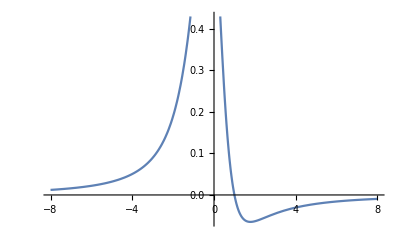

```mathematica
Plot[-(x (1+x))/(√2 (1+x^2)^(3/2))+1/(√2 √(1+x^2)),{x,-8,8}]
```

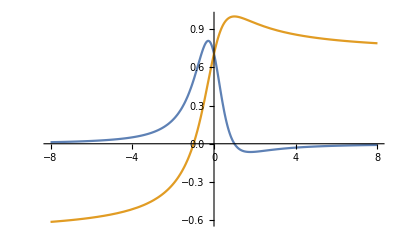

```mathematica
Plot[{-(x (1+x))/(√2 (1+x^2)^(3/2))+1/(√2 √(1+x^2)),(1+x)/(√2 √(1+x^2))},{x,-8,8}]
```

```mathematica
Solve[-(x (1+x))/(√2 (1+x^2)^(3/2))+1/(√2 √(1+x^2))==0,x,]
```

{{x→1}}

```mathematica
FullSimplify[Normalize@{x,x}.Normalize@{x,1/x},x∈Reals]
```

(1+x^2)/(√2 √(1+x^4))

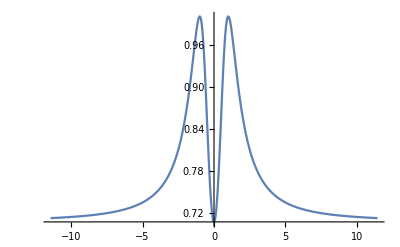

```mathematica
Plot[(1+x^2)/(√2 √(1+x^4)),{x,-11.440000000000001,11.440000000000001}]
```

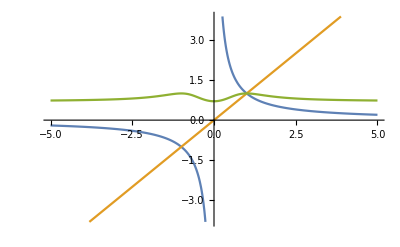

```mathematica
Plot[{1/x,x,(1+x^2)/(√2 √(1+x^4))},{x,-5,5}]
```

```mathematica
FullSimplify[Normalize@D[{x,x},x].Normalize@D[{x,1/x},x],x∈Reals]
```

(-1+x^2)/(√2 √(1+x^4))

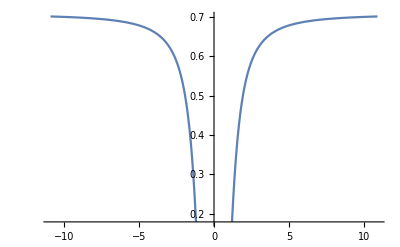

```mathematica
Plot[(-1+x^2)/(√2 √(1+x^4)),{x,-10.92,10.92}]
```

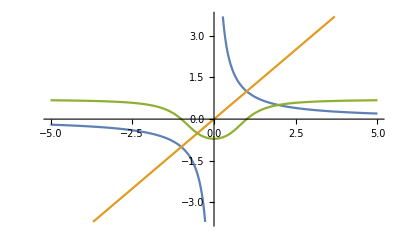

```mathematica
Plot[{1/x,x,(-1+x^2)/(√2 √(1+x^4))},{x,-5,5}]
```

```mathematica
-x+1
```

1-x

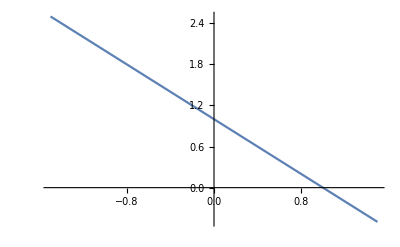

```mathematica
Plot[1-x,{x,-1.5,1.5}]
```

```mathematica
PDF[NormalDistribution[],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
ⅇ^(-x^2/2)
```

ⅇ^(-x^2/2)

```mathematica
(1-(ⅇ^(-x^2/2)))x+(ⅇ^(-x^2/2))(-x)
```

-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x

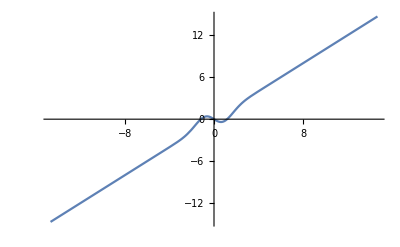

```mathematica
Plot[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x,{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
(1-(ⅇ^(-x^2/2)))((1-(ⅇ^(-(x-1)^2/2)))x+(ⅇ^(-(x-1)^2/2))(1-x))+(ⅇ^(-x^2/2))(-x)
```

-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (ⅇ^(-1/2 (-1+x)^2) (1-x)+(1-ⅇ^(-1/2 (-1+x)^2)) x)

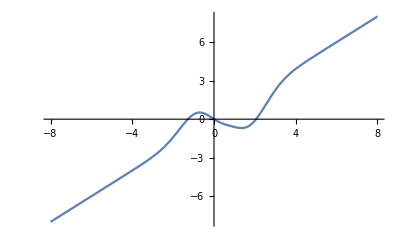

```mathematica
Plot[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (ⅇ^(-1/2 (-1+x)^2) (1-x)+(1-ⅇ^(-1/2 (-1+x)^2)) x),{x,-8,8}]
```

```mathematica
(1-(ⅇ^(-x^2/2)))((1-(ⅇ^(-(x-3)^2/2)))x+(ⅇ^(-(x-3)^2/2))(1-x))+(ⅇ^(-x^2/2))(-x)
```

-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (ⅇ^(-1/2 (-3+x)^2) (1-x)+(1-ⅇ^(-1/2 (-3+x)^2)) x)

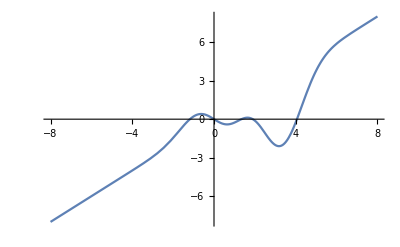

```mathematica
Plot[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) (ⅇ^(-1/2 (-3+x)^2) (1-x)+(1-ⅇ^(-1/2 (-3+x)^2)) x),{x,-8,8}]
```

```mathematica
(1-(ⅇ^(-x^2/2)))((1-(ⅇ^(-(x-3)^2/2)))x+(ⅇ^(-(x-3)^2/2))(x^2))+(ⅇ^(-x^2/2))(-x)
```

-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) ((1-ⅇ^(-1/2 (-3+x)^2)) x+ⅇ^(-1/2 (-3+x)^2) x^2)

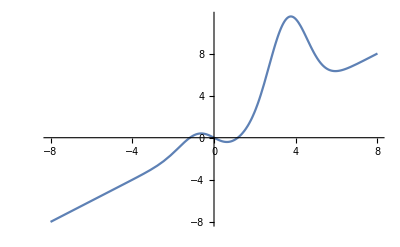

```mathematica
Plot[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) ((1-ⅇ^(-1/2 (-3+x)^2)) x+ⅇ^(-1/2 (-3+x)^2) x^2),{x,-8,8}]
```

```mathematica
InputForm[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) ((1-ⅇ^(-1/2 (-3+x)^2)) x+ⅇ^(-1/2 (-3+x)^2) x^2)]
```

-(x/E^(x^2/2)) + (1 - E^(-x^2/2))*((1 - E^(-(-3 + x)^2/2))*x + x^2/E^((-3 + x)^2/2))

```mathematica
FullForm[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) ((1-ⅇ^(-1/2 (-3+x)^2)) x+ⅇ^(-1/2 (-3+x)^2) x^2)]
```

Plus[Times[-1,Power[E,Times[Rational[-1,2],Power[x,2]]],x],Times[Plus[1,Times[-1,Power[E,Times[Rational[-1,2],Power[x,2]]]]],Plus[Times[Plus[1,Times[-1,Power[E,Times[Rational[-1,2],Power[Plus[-3,x],2]]]]],x],Times[Power[E,Times[Rational[-1,2],Power[Plus[-3,x],2]]],Power[x,2]]]]]

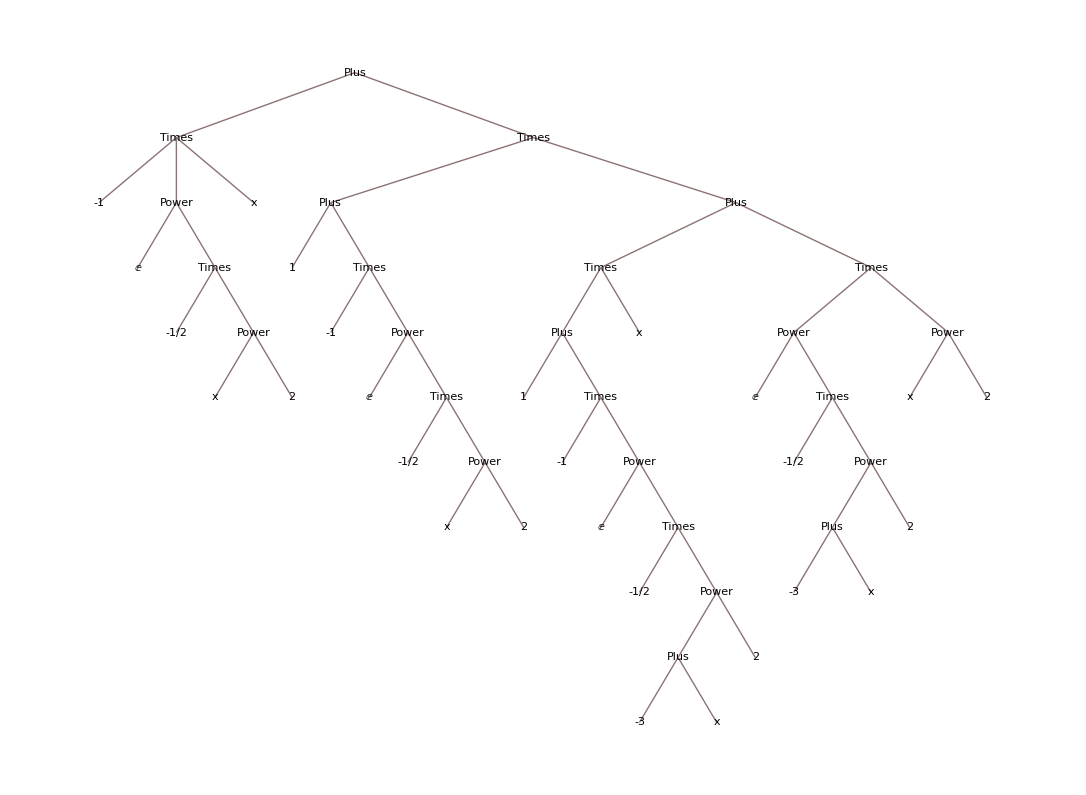

```mathematica
TreeForm[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) ((1-ⅇ^(-1/2 (-3+x)^2)) x+ⅇ^(-1/2 (-3+x)^2) x^2)]
```

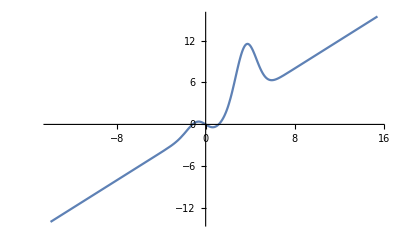

```mathematica
Plot[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) ((1-ⅇ^(-1/2 (-3+x)^2)) x+ⅇ^(-1/2 (-3+x)^2) x^2),{x,-13.946938456699069,15.446938456699069}]
```

```mathematica
(1-(ⅇ^(-x^2/2)))x^2+(ⅇ^(-x^2/2))(-x)
```

-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x^2

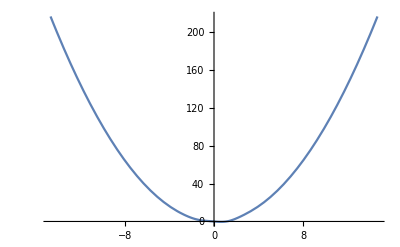

```mathematica
Plot[-ⅇ^(-x^2/2) x+(1-ⅇ^(-x^2/2)) x^2,{x,-14.696938456699069,14.696938456699069}]
```

```mathematica
Abs[x^3]-Abs[x]
```

-Abs[x]+Abs[x]^3

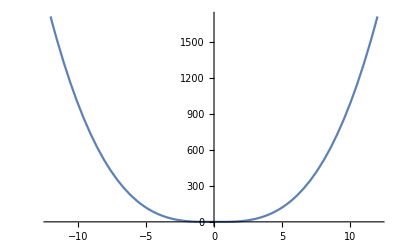

```mathematica
Plot[-Abs[x]+Abs[x]^3,{x,-12.,12.}]
```

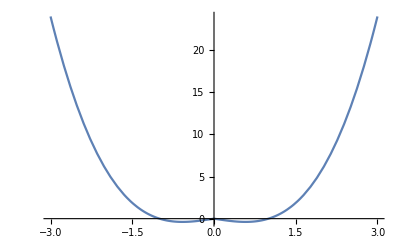

```mathematica
Plot[-Abs[x]+Abs[x]^3,{x,-3,3}]
```

```mathematica
Total@{Abs[x],Abs[x]^3}
```

Abs[x]+Abs[x]^3

```mathematica
{Abs[x],Abs[x]^3}/(Total@{Abs[x],Abs[x]^3})
```

{Abs[x]/(Abs[x]+Abs[x]^3),Abs[x]^3/(Abs[x]+Abs[x]^3)}

```mathematica
FullSimplify[{Abs[x],Abs[x]^3}/(Total@{Abs[x],Abs[x]^3}),x∈Reals]
```

{1/(1+x^2),x^2/(1+x^2)}

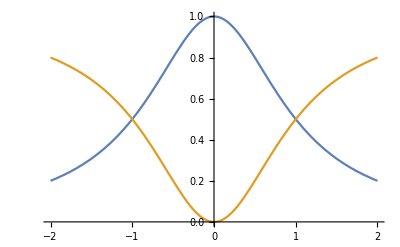

```mathematica
Plot[{1/(1+x^2),x^2/(1+x^2)},{x,-2,2}]
```

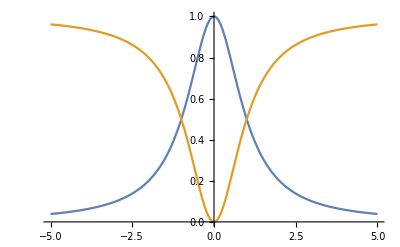

```mathematica
Plot[{1/(1+x^2),x^2/(1+x^2)},{x,-5,5}]
```

```mathematica
Solve[1/(1+x^2)==x^2/(1+x^2),x,]
```

{{x→1}}